{{100.,0.452384},{200.,0.393289},{300.,0.368811}}

{{100.,0.460906},{200.,0.484935},{300.,0.5}}

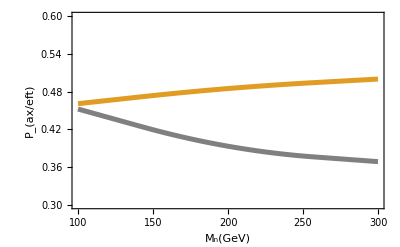

```mathematica
(* Correct mixing expression*)

Listax={{100.0,0.452384174},{200.0,0.393289477 },{300.0,0.368810564}}
Listeft={{100.0,0.460906088},{200.0,0.484934896 },{300.0,0.50}}

ListLinePlot[{Listax,Listeft},Frame->True,FrameLabel->{"M_n(GeV)","P_(ax/eft)"},LabelStyle->Directive[Bold,15],FrameTicksStyle->Directive[Black,15],RotateLabel -> True,PlotRange->{0.3,.6},PlotStyle->{{Gray,Thickness[0.009]},{Thickness[0.009]}},InterpolationOrder->2] (* FFilling->Axis,illingStyle->LightPink, *)
```